```mathematica
r020102[t_]:={{Cos[t],-Sin[t]},{Sin[t],Cos[t]}};
```

```mathematica
r0201[t_]:=r020102[t];
```

```mathematica
FullSimplify[Minimize[{Max[Abs[r0201[t][[1]][[1]]],Abs[r0201[t][[2]][[1]]]],t≥0,t≤Pi/2},t]]
```

{1/(√2),{t→π/4}}

```mathematica
r030102[t_]:={{Cos[t],-Sin[t],0},{Sin[t],Cos[t],0},{0,0,1}};
```

```mathematica
r030103[t_]:={{Cos[t],0,Sin[t]},{0,1,0},{-Sin[t],0,Cos[t]}};
```

```mathematica
r0301[t1_,t2_]:=r030102[t1].r030103[t2];
```

```mathematica
r0301[t1,t2]//MatrixForm
```

(Cos[t1] Cos[t2] | -Sin[t1] | Cos[t1] Sin[t2]
Cos[t2] Sin[t1] | Cos[t1] | Sin[t1] Sin[t2]
-Sin[t2] | 0 | Cos[t2])

```mathematica
NMinimize[Max[Abs[r0301[t1,t2][[1]][[1]]],Abs[r0301[t1,t2][[2]][[1]]],Abs[r0301[t1,t2][[3]][[1]]]],{t1,t2}]
```

{0.57735,{t1→0.785398,t2→0.61548}}

```mathematica
r040102[t_]:={{Cos[t],-Sin[t],0,0},{Sin[t],Cos[t],0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
r040103[t_]:={{Cos[t],0,Sin[t],0},{0,1,0,0},{-Sin[t],0,Cos[t],0},{0,0,0,1}};
```

```mathematica
r040104[t_]:={{Cos[t],0,0,-Sin[t]},{0,1,0,0},{0,0,1,0},{Sin[t],0,0,Cos[t]}};
```

```mathematica
r0401[t1_,t2_,t3_]:=r040102[t1].r040103[t2].r040104[t3];
```

```mathematica
r0401[t1,t2,t3]//MatrixForm
```

(Cos[t1] Cos[t2] Cos[t3] | -Sin[t1] | Cos[t1] Sin[t2] | -Cos[t1] Cos[t2] Sin[t3]
Cos[t2] Cos[t3] Sin[t1] | Cos[t1] | Sin[t1] Sin[t2] | -Cos[t2] Sin[t1] Sin[t3]
-Cos[t3] Sin[t2] | 0 | Cos[t2] | Sin[t2] Sin[t3]
Sin[t3] | 0 | 0 | Cos[t3])

```mathematica
NMinimize[Max[Abs[r0401[t1,t2,t3][[1]][[1]]],Abs[r0401[t1,t2,t3][[2]][[1]]],Abs[r0401[t1,t2,t3][[3]][[1]]],Abs[r0401[t1,t2,t3][[4]][[1]]]],{t1,t2,t3},Method->"DifferentialEvolution"]
```

{0.5,{t1→-0.785399,t2→-0.61548,t3→0.523599}}

```mathematica
r030203[t_]:={{1,0,0},{0,Cos[t],-Sin[t]},{0,Sin[t],Cos[t]}};
```

```mathematica
r030102[t1]//MatrixForm
```

(Cos[t1] | -Sin[t1] | 0
Sin[t1] | Cos[t1] | 0
0 | 0 | 1)

```mathematica
r030203[t2]//MatrixForm
```

(1 | 0 | 0
0 | Cos[t2] | -Sin[t2]
0 | Sin[t2] | Cos[t2])

```mathematica
r030103[t3]//MatrixForm
```

(Cos[t3] | 0 | Sin[t3]
0 | 1 | 0
-Sin[t3] | 0 | Cos[t3])

```mathematica
r0302[t1_,t2_,t3_]:=r030102[t1].r030203[t2].r030103[t3];
```

```mathematica
r0302[t1,t2,t3]//MatrixForm
```

(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3] | -Cos[t2] Sin[t1] | Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3]
Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3] | Cos[t1] Cos[t2] | -Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]
-Cos[t2] Sin[t3] | Sin[t2] | Cos[t2] Cos[t3])

```mathematica
r0302[t1,t2,0]//MatrixForm
```

(Cos[t1] | -Cos[t2] Sin[t1] | Sin[t1] Sin[t2]
Sin[t1] | Cos[t1] Cos[t2] | -Cos[t1] Sin[t2]
0 | Sin[t2] | Cos[t2])

```mathematica
Plot3D[{Abs[Cos[t1]]+Abs[-Sin[t1]Cos[t2]],Abs[Sin[t1]]+Abs[Cos[t1]Cos[t2]],Abs[Sin[t2]]},{t1,-Pi/2,Pi/2},{t2,-Pi/2,Pi/2},PlotRange->{0,1.5},PlotPoints->50,MaxRecursion->2,Exclusions->None,AxesLabel->{Style["t1",Bold,14],Style["t2",Bold,14]},PlotStyle->{{Red,Opacity[0.5]},{Green,Opacity[0.5]},{Blue,Opacity[0.5]}}]
```

-Graphics3D-

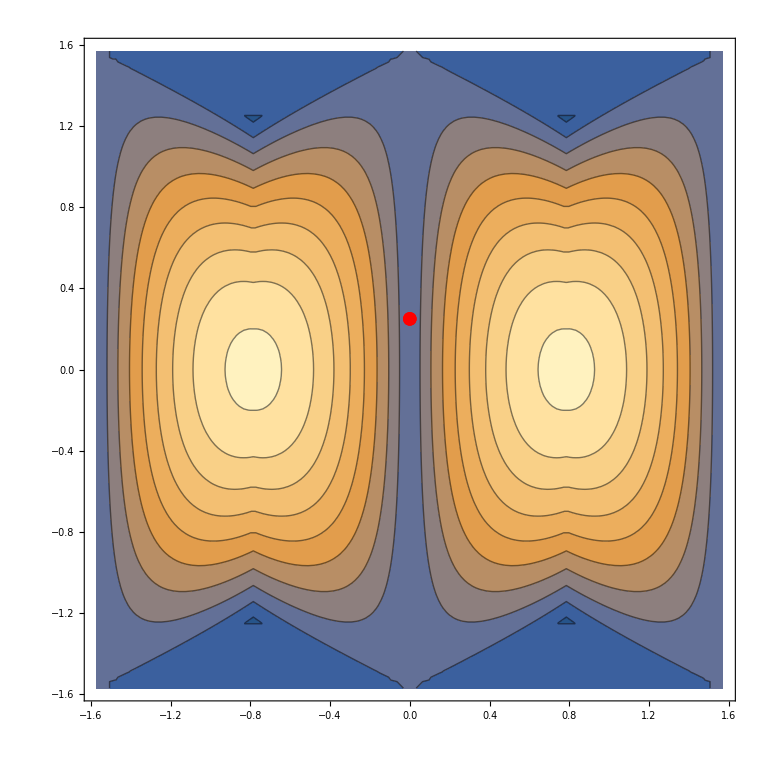

```mathematica
Show[ContourPlot[Max[Abs[Cos[t1]]+Abs[-Sin[t1]Cos[t2]],Abs[Sin[t1]]+Abs[Cos[t1]Cos[t2]],Abs[Sin[t2]]],{t1,-Pi/2,Pi/2},{t2,-Pi/2,Pi/2},PlotPoints->50,MaxRecursion->2,Exclusions->None],ListPlot[{{0.000000000000000115, 0.25}},Mesh->All,PlotStyle->Red]]
```

```mathematica
NMinimize[Max[Abs[Cos[t1]]+Abs[-Sin[t1]Cos[t2]],Abs[Sin[t1]]+Abs[Cos[t1]Cos[t2]],Abs[Sin[t2]]],{t1,t2}]
```

{0.942809,{t1→2.35619,t2→1.91063}}

```mathematica
N[{Abs[Cos[t1]]+Abs[-Sin[t1]Cos[t2]],Abs[Sin[t1]]+Abs[Cos[t1]Cos[t2]],Abs[Sin[t2]]}/.{t1->0,t2->1/4}]
```

{1.,0.968912,0.247404}

```mathematica
N[Sqrt[8/9]]
```

0.942809

```mathematica
D[Abs[Cos[t1]]+Abs[-Sin[t1]Cos[t2]],t1]
```

-Sin[t1] Abs'[Cos[t1]]+Cos[t1] Cos[t2] Abs'[Cos[t2] Sin[t1]]

```mathematica
N[D[Abs[Cos[t1]]+Abs[-Sin[t1]Cos[t2]],t1]/.{t1->Pi/4,t2->0.642829995288423439}]
```

0.56597 Abs'[0.56597]-0.707107 Abs'[0.707107]

```mathematica
:w`
```

```mathematica
D[Abs[Cos[t1]]+Abs[-Sin[t1]Cos[t2]],t2]
```

-Sin[t1] Sin[t2] Abs'[Cos[t2] Sin[t1]]

```mathematica
D[Abs[Sin[t1]]+Abs[Cos[t1]Cos[t2]],t1]
```

-Cos[t2] Sin[t1] Abs'[Cos[t1] Cos[t2]]+Cos[t1] Abs'[Sin[t1]]

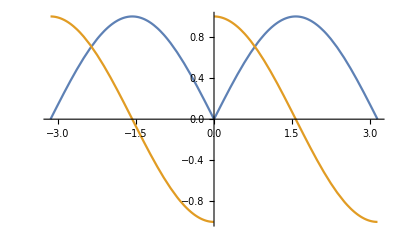

```mathematica
Plot[{Abs[Sin[t1]],Cos[t1](2UnitStep[Sin[t1]]-1)},{t1,-Pi,Pi}]
```

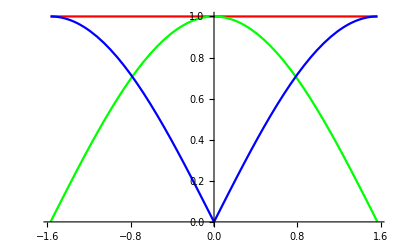

```mathematica
Plot[{Abs[Cos[t1]]+Abs[-Sin[t1]Cos[t2]]/.t1->0,Abs[Sin[t1]]+Abs[Cos[t1]Cos[t2]]/.t1->0,Abs[Sin[t2]]/.t1->0},{t2,-Pi/2,Pi/2},PlotStyle->{Red,Green,Blue}]
```

```mathematica
r0302[t1,t2,t3]//MatrixForm
```

(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3] | -Cos[t2] Sin[t1] | Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3]
Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3] | Cos[t1] Cos[t2] | -Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]
-Cos[t2] Sin[t3] | Sin[t2] | Cos[t2] Cos[t3])

```mathematica
r0302[t1,t2,0]//MatrixForm
```

(Cos[t1] | -Cos[t2] Sin[t1] | Sin[t1] Sin[t2]
Sin[t1] | Cos[t1] Cos[t2] | -Cos[t1] Sin[t2]
0 | Sin[t2] | Cos[t2])

```mathematica
r0302[t1,0,t3]//MatrixForm
```

(Cos[t1] Cos[t3] | -Sin[t1] | Cos[t1] Sin[t3]
Cos[t3] Sin[t1] | Cos[t1] | Sin[t1] Sin[t3]
-Sin[t3] | 0 | Cos[t3])

```mathematica
r0302[Pi/2,t2,t3]//MatrixForm
```

(-Sin[t2] Sin[t3] | -Cos[t2] | Cos[t3] Sin[t2]
Cos[t3] | 0 | Sin[t3]
-Cos[t2] Sin[t3] | Sin[t2] | Cos[t2] Cos[t3])

```mathematica
r0302[t1,Pi/2,t3]//MatrixForm
```

(Cos[t1] Cos[t3]-Sin[t1] Sin[t3] | 0 | Cos[t3] Sin[t1]+Cos[t1] Sin[t3]
Cos[t3] Sin[t1]+Cos[t1] Sin[t3] | 0 | -Cos[t1] Cos[t3]+Sin[t1] Sin[t3]
0 | 1 | 0)

```mathematica
r0302[0,t2,t3]//MatrixForm
```

(Cos[t3] | 0 | Sin[t3]
Sin[t2] Sin[t3] | Cos[t2] | -Cos[t3] Sin[t2]
-Cos[t2] Sin[t3] | Sin[t2] | Cos[t2] Cos[t3])

```mathematica
Solve[Sin[t1]Cos[t3]+Cos[t1]Sin[t2]Sin[t3]==0,t3]
```

{{t3→ConditionalExpression[ArcTan[-(Cos[t1] Sin[t2])/(√(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2)),Sin[t1]/(√(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2))]+2 π C[1],C[1]∈ℤ]},{t3→ConditionalExpression[ArcTan[(Cos[t1] Sin[t2])/(√(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2)),-Sin[t1]/(√(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2))]+2 π C[1],C[1]∈ℤ]}}

```mathematica
FullSimplify[r0302[t1,t2,ArcTan[-(Cos[t1] Sin[t2])/(√(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2)),Sin[t1]/(√(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2))]]]//MatrixForm
```

(-Sin[t2]/(√(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2)) | -Cos[t2] Sin[t1] | (Cos[t1] Cos[t2]^2 Sin[t1])/(√(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2))
0 | Cos[t1] Cos[t2] | √(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2)
-(Cos[t2] Sin[t1])/(√(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2)) | Sin[t2] | -(Cos[t1] Cos[t2] Sin[t2])/(√(Sin[t1]^2+Cos[t1]^2 Sin[t2]^2)))

```mathematica
Solve[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]==0,t3]
```

{{t3→ConditionalExpression[ArcTan[-(Sin[t1] Sin[t2])/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2)),-Cos[t1]/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2))]+2 π C[1],C[1]∈ℤ]},{t3→ConditionalExpression[ArcTan[(Sin[t1] Sin[t2])/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2)),Cos[t1]/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2))]+2 π C[1],C[1]∈ℤ]}}

```mathematica
FullSimplify[r0302[t1,t2,ArcTan[-(Sin[t1] Sin[t2])/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2)),-Cos[t1]/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2))]]]//MatrixForm
```

(0 | -Cos[t2] Sin[t1] | -√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2)
-Sin[t2]/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2)) | Cos[t1] Cos[t2] | -(Cos[t1] Cos[t2]^2 Sin[t1])/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2))
(Cos[t1] Cos[t2])/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2)) | Sin[t2] | -(Cos[t2] Sin[t1] Sin[t2])/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2)))

```mathematica
Solve[-Cos[t2]Sin[t1]==Sqrt[8/9],t2]
```

{{t2→ConditionalExpression[-ArcCos[-2/3 √2 Csc[t1]]+2 π C[1],C[1]∈ℤ]},{t2→ConditionalExpression[ArcCos[-2/3 √2 Csc[t1]]+2 π C[1],C[1]∈ℤ]}}

```mathematica
FullSimplify[r0302[t1,t2,ArcTan[-(Sin[t1] Sin[t2])/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2)),-Cos[t1]/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2))]]/.t2->ArcCos[-2/3 √2 Csc[t1]]]//MatrixForm
```

(0 | (2 √2)/3 | -1/3
-√(9-8 Csc[t1]^2) | -2/3 √2 Cot[t1] | -(8 Cot[t1])/3
-2 √2 Cot[t1] | √(1-(8 Csc[t1]^2)/9) | 2/3 √2 √(9-8 Csc[t1]^2))

```mathematica
Solve[√(9-8 Csc[t1]^2)==Sqrt[2]/2,t1]
```

{{t1→ConditionalExpression[-ArcSin[4/(√17)]+2 π C[1],C[1]∈ℤ]},{t1→ConditionalExpression[π-ArcSin[4/(√17)]+2 π C[1],C[1]∈ℤ]},{t1→ConditionalExpression[ArcSin[4/(√17)]+2 π C[1],C[1]∈ℤ]},{t1→ConditionalExpression[π+ArcSin[4/(√17)]+2 π C[1],C[1]∈ℤ]}}

```mathematica
soln=FullSimplify[(r0302[t1,t2,ArcTan[-(Sin[t1] Sin[t2])/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2)),-Cos[t1]/(√(Cos[t1]^2+Sin[t1]^2 Sin[t2]^2))]]/.t2->ArcCos[-2/3 √2 Csc[t1]])/.t1->ArcSin[4/(√17)]]//MatrixForm
```

(0 | (2 √2)/3 | -1/3
-1/(√2) | -1/(3 √2) | -2/3
-1/(√2) | 1/(3 √2) | 2/3)

```mathematica
N[soln]
```

(0. | 0.942809 | -0.333333
-0.707107 | -0.235702 | -0.666667
-0.707107 | 0.235702 | 0.666667)

```mathematica
rota[t_,n_,n1_,n2_]:=Module[{mat},mat=IdentityMatrix[n];mat[[n1]][[n1]]=Cos[t];mat[[n2]][[n2]]=Cos[t];mat[[n1]][[n2]]=-Sin[t];mat[[n2]][[n1]]=Sin[t];mat]
```

```mathematica
rota[t1,11,1,2]//MatrixForm
```

(Cos[t1] | -Sin[t1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[t1] | Cos[t1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
r1103=rota[t0102,11,1,2].rota[t0103,11,1,3].rota[t0104,11,1,4].rota[t0105,11,1,5].rota[t0106,11,1,6].rota[t0107,11,1,7].rota[t0108,11,1,8].rota[t0109,11,1,9].rota[t0110,11,1,10].rota[t0111,11,1,11].rota[t0203,11,2,3].rota[t0204,11,2,4].rota[t0205,11,2,5].rota[t0206,11,2,6].rota[t0207,11,2,7].rota[t0208,11,2,8].rota[t0209,11,2,9].rota[t0210,11,2,10].rota[t0211,11,2,11].rota[t0304,11,3,4].rota[t0305,11,3,5].rota[t0306,11,3,6].rota[t0307,11,3,7].rota[t0308,11,3,8].rota[t0309,11,3,9].rota[t0310,11,3,10].rota[t0311,11,3,11];
```

```mathematica
r1103[[1;;11,1]]//MatrixForm
```

(Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0111]
Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0111] Sin[t0102]
Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0111] Sin[t0103]
Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0111] Sin[t0104]
Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0111] Sin[t0105]
Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0111] Sin[t0106]
Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0111] Sin[t0107]
Cos[t0109] Cos[t0110] Cos[t0111] Sin[t0108]
Cos[t0110] Cos[t0111] Sin[t0109]
Cos[t0111] Sin[t0110]
Sin[t0111])

```mathematica
r1103[[1;;11,2]]//MatrixForm
```

(Cos[t0211] (Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0204] (-Cos[t0203] Sin[t0102]-Cos[t0102] Sin[t0103] Sin[t0203])-Cos[t0102] Cos[t0103] Sin[t0104] Sin[t0204])-Cos[t0102] Cos[t0103] Cos[t0104] Sin[t0105] Sin[t0205])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0106] Sin[t0206])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0107] Sin[t0207])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0108] Sin[t0208])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0109] Sin[t0209])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0110] Sin[t0210])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Sin[t0111] Sin[t0211]
Cos[t0211] (Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0204] (Cos[t0102] Cos[t0203]-Sin[t0102] Sin[t0103] Sin[t0203])-Cos[t0103] Sin[t0102] Sin[t0104] Sin[t0204])-Cos[t0103] Cos[t0104] Sin[t0102] Sin[t0105] Sin[t0205])-Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0102] Sin[t0106] Sin[t0206])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0102] Sin[t0107] Sin[t0207])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0102] Sin[t0108] Sin[t0208])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0102] Sin[t0109] Sin[t0209])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0102] Sin[t0110] Sin[t0210])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Sin[t0102] Sin[t0111] Sin[t0211]
Cos[t0211] (Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0103] Cos[t0204] Sin[t0203]-Sin[t0103] Sin[t0104] Sin[t0204])-Cos[t0104] Sin[t0103] Sin[t0105] Sin[t0205])-Cos[t0104] Cos[t0105] Sin[t0103] Sin[t0106] Sin[t0206])-Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0103] Sin[t0107] Sin[t0207])-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0103] Sin[t0108] Sin[t0208])-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0103] Sin[t0109] Sin[t0209])-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0103] Sin[t0110] Sin[t0210])-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Sin[t0103] Sin[t0111] Sin[t0211]
Cos[t0211] (Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0104] Cos[t0205] Sin[t0204]-Sin[t0104] Sin[t0105] Sin[t0205])-Cos[t0105] Sin[t0104] Sin[t0106] Sin[t0206])-Cos[t0105] Cos[t0106] Sin[t0104] Sin[t0107] Sin[t0207])-Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0104] Sin[t0108] Sin[t0208])-Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0104] Sin[t0109] Sin[t0209])-Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0104] Sin[t0110] Sin[t0210])-Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Sin[t0104] Sin[t0111] Sin[t0211]
Cos[t0211] (Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0105] Cos[t0206] Sin[t0205]-Sin[t0105] Sin[t0106] Sin[t0206])-Cos[t0106] Sin[t0105] Sin[t0107] Sin[t0207])-Cos[t0106] Cos[t0107] Sin[t0105] Sin[t0108] Sin[t0208])-Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0105] Sin[t0109] Sin[t0209])-Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0105] Sin[t0110] Sin[t0210])-Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Sin[t0105] Sin[t0111] Sin[t0211]
Cos[t0211] (Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0106] Cos[t0207] Sin[t0206]-Sin[t0106] Sin[t0107] Sin[t0207])-Cos[t0107] Sin[t0106] Sin[t0108] Sin[t0208])-Cos[t0107] Cos[t0108] Sin[t0106] Sin[t0109] Sin[t0209])-Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0106] Sin[t0110] Sin[t0210])-Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Sin[t0106] Sin[t0111] Sin[t0211]
Cos[t0211] (Cos[t0210] (Cos[t0209] (Cos[t0107] Cos[t0208] Sin[t0207]-Sin[t0107] Sin[t0108] Sin[t0208])-Cos[t0108] Sin[t0107] Sin[t0109] Sin[t0209])-Cos[t0108] Cos[t0109] Sin[t0107] Sin[t0110] Sin[t0210])-Cos[t0108] Cos[t0109] Cos[t0110] Sin[t0107] Sin[t0111] Sin[t0211]
Cos[t0211] (Cos[t0210] (Cos[t0108] Cos[t0209] Sin[t0208]-Sin[t0108] Sin[t0109] Sin[t0209])-Cos[t0109] Sin[t0108] Sin[t0110] Sin[t0210])-Cos[t0109] Cos[t0110] Sin[t0108] Sin[t0111] Sin[t0211]
Cos[t0211] (Cos[t0109] Cos[t0210] Sin[t0209]-Sin[t0109] Sin[t0110] Sin[t0210])-Cos[t0110] Sin[t0109] Sin[t0111] Sin[t0211]
Cos[t0110] Cos[t0211] Sin[t0210]-Sin[t0110] Sin[t0111] Sin[t0211]
Cos[t0111] Sin[t0211])

```mathematica
r1103[[9,2]]
```

Cos[t0211] (Cos[t0109] Cos[t0210] Sin[t0209]-Sin[t0109] Sin[t0110] Sin[t0210])-Cos[t0110] Sin[t0109] Sin[t0111] Sin[t0211]

```mathematica
r1103[[10,2]]
```

Cos[t0110] Cos[t0211] Sin[t0210]-Sin[t0110] Sin[t0111] Sin[t0211]

```mathematica
r1103[[11,2]]
```

Cos[t0111] Sin[t0211]

```mathematica
r1103[[1;;11,3]]//MatrixForm
```

(Cos[t0311] (Cos[t0310] (Cos[t0309] (Cos[t0308] (Cos[t0307] (Cos[t0306] (Cos[t0305] (Cos[t0304] (-Cos[t0102] Cos[t0203] Sin[t0103]+Sin[t0102] Sin[t0203])+(-Cos[t0102] Cos[t0103] Cos[t0204] Sin[t0104]-(-Cos[t0203] Sin[t0102]-Cos[t0102] Sin[t0103] Sin[t0203]) Sin[t0204]) Sin[t0304])+(-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0205] Sin[t0105]-(Cos[t0204] (-Cos[t0203] Sin[t0102]-Cos[t0102] Sin[t0103] Sin[t0203])-Cos[t0102] Cos[t0103] Sin[t0104] Sin[t0204]) Sin[t0205]) Sin[t0305])+(-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0206] Sin[t0106]-(Cos[t0205] (Cos[t0204] (-Cos[t0203] Sin[t0102]-Cos[t0102] Sin[t0103] Sin[t0203])-Cos[t0102] Cos[t0103] Sin[t0104] Sin[t0204])-Cos[t0102] Cos[t0103] Cos[t0104] Sin[t0105] Sin[t0205]) Sin[t0206]) Sin[t0306])+(-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0207] Sin[t0107]-(Cos[t0206] (Cos[t0205] (Cos[t0204] (-Cos[t0203] Sin[t0102]-Cos[t0102] Sin[t0103] Sin[t0203])-Cos[t0102] Cos[t0103] Sin[t0104] Sin[t0204])-Cos[t0102] Cos[t0103] Cos[t0104] Sin[t0105] Sin[t0205])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0106] Sin[t0206]) Sin[t0207]) Sin[t0307])+(-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0208] Sin[t0108]-(Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0204] (-Cos[t0203] Sin[t0102]-Cos[t0102] Sin[t0103] Sin[t0203])-Cos[t0102] Cos[t0103] Sin[t0104] Sin[t0204])-Cos[t0102] Cos[t0103] Cos[t0104] Sin[t0105] Sin[t0205])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0106] Sin[t0206])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0107] Sin[t0207]) Sin[t0208]) Sin[t0308])+(-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0209] Sin[t0109]-(Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0204] (-Cos[t0203] Sin[t0102]-Cos[t0102] Sin[t0103] Sin[t0203])-Cos[t0102] Cos[t0103] Sin[t0104] Sin[t0204])-Cos[t0102] Cos[t0103] Cos[t0104] Sin[t0105] Sin[t0205])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0106] Sin[t0206])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0107] Sin[t0207])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0108] Sin[t0208]) Sin[t0209]) Sin[t0309])+(-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0210] Sin[t0110]-(Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0204] (-Cos[t0203] Sin[t0102]-Cos[t0102] Sin[t0103] Sin[t0203])-Cos[t0102] Cos[t0103] Sin[t0104] Sin[t0204])-Cos[t0102] Cos[t0103] Cos[t0104] Sin[t0105] Sin[t0205])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0106] Sin[t0206])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0107] Sin[t0207])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0108] Sin[t0208])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0109] Sin[t0209]) Sin[t0210]) Sin[t0310])+(-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0211] Sin[t0111]-(Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0204] (-Cos[t0203] Sin[t0102]-Cos[t0102] Sin[t0103] Sin[t0203])-Cos[t0102] Cos[t0103] Sin[t0104] Sin[t0204])-Cos[t0102] Cos[t0103] Cos[t0104] Sin[t0105] Sin[t0205])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0106] Sin[t0206])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0107] Sin[t0207])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0108] Sin[t0208])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0109] Sin[t0209])-Cos[t0102] Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0110] Sin[t0210]) Sin[t0211]) Sin[t0311]
Cos[t0311] (Cos[t0310] (Cos[t0309] (Cos[t0308] (Cos[t0307] (Cos[t0306] (Cos[t0305] (Cos[t0304] (-Cos[t0203] Sin[t0102] Sin[t0103]-Cos[t0102] Sin[t0203])+(-Cos[t0103] Cos[t0204] Sin[t0102] Sin[t0104]-(Cos[t0102] Cos[t0203]-Sin[t0102] Sin[t0103] Sin[t0203]) Sin[t0204]) Sin[t0304])+(-Cos[t0103] Cos[t0104] Cos[t0205] Sin[t0102] Sin[t0105]-(Cos[t0204] (Cos[t0102] Cos[t0203]-Sin[t0102] Sin[t0103] Sin[t0203])-Cos[t0103] Sin[t0102] Sin[t0104] Sin[t0204]) Sin[t0205]) Sin[t0305])+(-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0206] Sin[t0102] Sin[t0106]-(Cos[t0205] (Cos[t0204] (Cos[t0102] Cos[t0203]-Sin[t0102] Sin[t0103] Sin[t0203])-Cos[t0103] Sin[t0102] Sin[t0104] Sin[t0204])-Cos[t0103] Cos[t0104] Sin[t0102] Sin[t0105] Sin[t0205]) Sin[t0206]) Sin[t0306])+(-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0207] Sin[t0102] Sin[t0107]-(Cos[t0206] (Cos[t0205] (Cos[t0204] (Cos[t0102] Cos[t0203]-Sin[t0102] Sin[t0103] Sin[t0203])-Cos[t0103] Sin[t0102] Sin[t0104] Sin[t0204])-Cos[t0103] Cos[t0104] Sin[t0102] Sin[t0105] Sin[t0205])-Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0102] Sin[t0106] Sin[t0206]) Sin[t0207]) Sin[t0307])+(-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0208] Sin[t0102] Sin[t0108]-(Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0204] (Cos[t0102] Cos[t0203]-Sin[t0102] Sin[t0103] Sin[t0203])-Cos[t0103] Sin[t0102] Sin[t0104] Sin[t0204])-Cos[t0103] Cos[t0104] Sin[t0102] Sin[t0105] Sin[t0205])-Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0102] Sin[t0106] Sin[t0206])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0102] Sin[t0107] Sin[t0207]) Sin[t0208]) Sin[t0308])+(-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0209] Sin[t0102] Sin[t0109]-(Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0204] (Cos[t0102] Cos[t0203]-Sin[t0102] Sin[t0103] Sin[t0203])-Cos[t0103] Sin[t0102] Sin[t0104] Sin[t0204])-Cos[t0103] Cos[t0104] Sin[t0102] Sin[t0105] Sin[t0205])-Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0102] Sin[t0106] Sin[t0206])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0102] Sin[t0107] Sin[t0207])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0102] Sin[t0108] Sin[t0208]) Sin[t0209]) Sin[t0309])+(-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0210] Sin[t0102] Sin[t0110]-(Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0204] (Cos[t0102] Cos[t0203]-Sin[t0102] Sin[t0103] Sin[t0203])-Cos[t0103] Sin[t0102] Sin[t0104] Sin[t0204])-Cos[t0103] Cos[t0104] Sin[t0102] Sin[t0105] Sin[t0205])-Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0102] Sin[t0106] Sin[t0206])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0102] Sin[t0107] Sin[t0207])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0102] Sin[t0108] Sin[t0208])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0102] Sin[t0109] Sin[t0209]) Sin[t0210]) Sin[t0310])+(-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0211] Sin[t0102] Sin[t0111]-(Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0204] (Cos[t0102] Cos[t0203]-Sin[t0102] Sin[t0103] Sin[t0203])-Cos[t0103] Sin[t0102] Sin[t0104] Sin[t0204])-Cos[t0103] Cos[t0104] Sin[t0102] Sin[t0105] Sin[t0205])-Cos[t0103] Cos[t0104] Cos[t0105] Sin[t0102] Sin[t0106] Sin[t0206])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0102] Sin[t0107] Sin[t0207])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0102] Sin[t0108] Sin[t0208])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0102] Sin[t0109] Sin[t0209])-Cos[t0103] Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0102] Sin[t0110] Sin[t0210]) Sin[t0211]) Sin[t0311]
Cos[t0311] (Cos[t0310] (Cos[t0309] (Cos[t0308] (Cos[t0307] (Cos[t0306] (Cos[t0305] (Cos[t0103] Cos[t0203] Cos[t0304]+(-Cos[t0204] Sin[t0103] Sin[t0104]-Cos[t0103] Sin[t0203] Sin[t0204]) Sin[t0304])+(-Cos[t0104] Cos[t0205] Sin[t0103] Sin[t0105]-(Cos[t0103] Cos[t0204] Sin[t0203]-Sin[t0103] Sin[t0104] Sin[t0204]) Sin[t0205]) Sin[t0305])+(-Cos[t0104] Cos[t0105] Cos[t0206] Sin[t0103] Sin[t0106]-(Cos[t0205] (Cos[t0103] Cos[t0204] Sin[t0203]-Sin[t0103] Sin[t0104] Sin[t0204])-Cos[t0104] Sin[t0103] Sin[t0105] Sin[t0205]) Sin[t0206]) Sin[t0306])+(-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0207] Sin[t0103] Sin[t0107]-(Cos[t0206] (Cos[t0205] (Cos[t0103] Cos[t0204] Sin[t0203]-Sin[t0103] Sin[t0104] Sin[t0204])-Cos[t0104] Sin[t0103] Sin[t0105] Sin[t0205])-Cos[t0104] Cos[t0105] Sin[t0103] Sin[t0106] Sin[t0206]) Sin[t0207]) Sin[t0307])+(-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0208] Sin[t0103] Sin[t0108]-(Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0103] Cos[t0204] Sin[t0203]-Sin[t0103] Sin[t0104] Sin[t0204])-Cos[t0104] Sin[t0103] Sin[t0105] Sin[t0205])-Cos[t0104] Cos[t0105] Sin[t0103] Sin[t0106] Sin[t0206])-Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0103] Sin[t0107] Sin[t0207]) Sin[t0208]) Sin[t0308])+(-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0209] Sin[t0103] Sin[t0109]-(Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0103] Cos[t0204] Sin[t0203]-Sin[t0103] Sin[t0104] Sin[t0204])-Cos[t0104] Sin[t0103] Sin[t0105] Sin[t0205])-Cos[t0104] Cos[t0105] Sin[t0103] Sin[t0106] Sin[t0206])-Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0103] Sin[t0107] Sin[t0207])-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0103] Sin[t0108] Sin[t0208]) Sin[t0209]) Sin[t0309])+(-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0210] Sin[t0103] Sin[t0110]-(Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0103] Cos[t0204] Sin[t0203]-Sin[t0103] Sin[t0104] Sin[t0204])-Cos[t0104] Sin[t0103] Sin[t0105] Sin[t0205])-Cos[t0104] Cos[t0105] Sin[t0103] Sin[t0106] Sin[t0206])-Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0103] Sin[t0107] Sin[t0207])-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0103] Sin[t0108] Sin[t0208])-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0103] Sin[t0109] Sin[t0209]) Sin[t0210]) Sin[t0310])+(-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0211] Sin[t0103] Sin[t0111]-(Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0205] (Cos[t0103] Cos[t0204] Sin[t0203]-Sin[t0103] Sin[t0104] Sin[t0204])-Cos[t0104] Sin[t0103] Sin[t0105] Sin[t0205])-Cos[t0104] Cos[t0105] Sin[t0103] Sin[t0106] Sin[t0206])-Cos[t0104] Cos[t0105] Cos[t0106] Sin[t0103] Sin[t0107] Sin[t0207])-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0103] Sin[t0108] Sin[t0208])-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0103] Sin[t0109] Sin[t0209])-Cos[t0104] Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0103] Sin[t0110] Sin[t0210]) Sin[t0211]) Sin[t0311]
Cos[t0311] (Cos[t0310] (Cos[t0309] (Cos[t0308] (Cos[t0307] (Cos[t0306] (Cos[t0104] Cos[t0204] Cos[t0305] Sin[t0304]+(-Cos[t0205] Sin[t0104] Sin[t0105]-Cos[t0104] Sin[t0204] Sin[t0205]) Sin[t0305])+(-Cos[t0105] Cos[t0206] Sin[t0104] Sin[t0106]-(Cos[t0104] Cos[t0205] Sin[t0204]-Sin[t0104] Sin[t0105] Sin[t0205]) Sin[t0206]) Sin[t0306])+(-Cos[t0105] Cos[t0106] Cos[t0207] Sin[t0104] Sin[t0107]-(Cos[t0206] (Cos[t0104] Cos[t0205] Sin[t0204]-Sin[t0104] Sin[t0105] Sin[t0205])-Cos[t0105] Sin[t0104] Sin[t0106] Sin[t0206]) Sin[t0207]) Sin[t0307])+(-Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0208] Sin[t0104] Sin[t0108]-(Cos[t0207] (Cos[t0206] (Cos[t0104] Cos[t0205] Sin[t0204]-Sin[t0104] Sin[t0105] Sin[t0205])-Cos[t0105] Sin[t0104] Sin[t0106] Sin[t0206])-Cos[t0105] Cos[t0106] Sin[t0104] Sin[t0107] Sin[t0207]) Sin[t0208]) Sin[t0308])+(-Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0209] Sin[t0104] Sin[t0109]-(Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0104] Cos[t0205] Sin[t0204]-Sin[t0104] Sin[t0105] Sin[t0205])-Cos[t0105] Sin[t0104] Sin[t0106] Sin[t0206])-Cos[t0105] Cos[t0106] Sin[t0104] Sin[t0107] Sin[t0207])-Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0104] Sin[t0108] Sin[t0208]) Sin[t0209]) Sin[t0309])+(-Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0210] Sin[t0104] Sin[t0110]-(Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0104] Cos[t0205] Sin[t0204]-Sin[t0104] Sin[t0105] Sin[t0205])-Cos[t0105] Sin[t0104] Sin[t0106] Sin[t0206])-Cos[t0105] Cos[t0106] Sin[t0104] Sin[t0107] Sin[t0207])-Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0104] Sin[t0108] Sin[t0208])-Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0104] Sin[t0109] Sin[t0209]) Sin[t0210]) Sin[t0310])+(-Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0211] Sin[t0104] Sin[t0111]-(Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0206] (Cos[t0104] Cos[t0205] Sin[t0204]-Sin[t0104] Sin[t0105] Sin[t0205])-Cos[t0105] Sin[t0104] Sin[t0106] Sin[t0206])-Cos[t0105] Cos[t0106] Sin[t0104] Sin[t0107] Sin[t0207])-Cos[t0105] Cos[t0106] Cos[t0107] Sin[t0104] Sin[t0108] Sin[t0208])-Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0104] Sin[t0109] Sin[t0209])-Cos[t0105] Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0104] Sin[t0110] Sin[t0210]) Sin[t0211]) Sin[t0311]
Cos[t0311] (Cos[t0310] (Cos[t0309] (Cos[t0308] (Cos[t0307] (Cos[t0105] Cos[t0205] Cos[t0306] Sin[t0305]+(-Cos[t0206] Sin[t0105] Sin[t0106]-Cos[t0105] Sin[t0205] Sin[t0206]) Sin[t0306])+(-Cos[t0106] Cos[t0207] Sin[t0105] Sin[t0107]-(Cos[t0105] Cos[t0206] Sin[t0205]-Sin[t0105] Sin[t0106] Sin[t0206]) Sin[t0207]) Sin[t0307])+(-Cos[t0106] Cos[t0107] Cos[t0208] Sin[t0105] Sin[t0108]-(Cos[t0207] (Cos[t0105] Cos[t0206] Sin[t0205]-Sin[t0105] Sin[t0106] Sin[t0206])-Cos[t0106] Sin[t0105] Sin[t0107] Sin[t0207]) Sin[t0208]) Sin[t0308])+(-Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0209] Sin[t0105] Sin[t0109]-(Cos[t0208] (Cos[t0207] (Cos[t0105] Cos[t0206] Sin[t0205]-Sin[t0105] Sin[t0106] Sin[t0206])-Cos[t0106] Sin[t0105] Sin[t0107] Sin[t0207])-Cos[t0106] Cos[t0107] Sin[t0105] Sin[t0108] Sin[t0208]) Sin[t0209]) Sin[t0309])+(-Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0210] Sin[t0105] Sin[t0110]-(Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0105] Cos[t0206] Sin[t0205]-Sin[t0105] Sin[t0106] Sin[t0206])-Cos[t0106] Sin[t0105] Sin[t0107] Sin[t0207])-Cos[t0106] Cos[t0107] Sin[t0105] Sin[t0108] Sin[t0208])-Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0105] Sin[t0109] Sin[t0209]) Sin[t0210]) Sin[t0310])+(-Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0211] Sin[t0105] Sin[t0111]-(Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0207] (Cos[t0105] Cos[t0206] Sin[t0205]-Sin[t0105] Sin[t0106] Sin[t0206])-Cos[t0106] Sin[t0105] Sin[t0107] Sin[t0207])-Cos[t0106] Cos[t0107] Sin[t0105] Sin[t0108] Sin[t0208])-Cos[t0106] Cos[t0107] Cos[t0108] Sin[t0105] Sin[t0109] Sin[t0209])-Cos[t0106] Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0105] Sin[t0110] Sin[t0210]) Sin[t0211]) Sin[t0311]
Cos[t0311] (Cos[t0310] (Cos[t0309] (Cos[t0308] (Cos[t0106] Cos[t0206] Cos[t0307] Sin[t0306]+(-Cos[t0207] Sin[t0106] Sin[t0107]-Cos[t0106] Sin[t0206] Sin[t0207]) Sin[t0307])+(-Cos[t0107] Cos[t0208] Sin[t0106] Sin[t0108]-(Cos[t0106] Cos[t0207] Sin[t0206]-Sin[t0106] Sin[t0107] Sin[t0207]) Sin[t0208]) Sin[t0308])+(-Cos[t0107] Cos[t0108] Cos[t0209] Sin[t0106] Sin[t0109]-(Cos[t0208] (Cos[t0106] Cos[t0207] Sin[t0206]-Sin[t0106] Sin[t0107] Sin[t0207])-Cos[t0107] Sin[t0106] Sin[t0108] Sin[t0208]) Sin[t0209]) Sin[t0309])+(-Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0210] Sin[t0106] Sin[t0110]-(Cos[t0209] (Cos[t0208] (Cos[t0106] Cos[t0207] Sin[t0206]-Sin[t0106] Sin[t0107] Sin[t0207])-Cos[t0107] Sin[t0106] Sin[t0108] Sin[t0208])-Cos[t0107] Cos[t0108] Sin[t0106] Sin[t0109] Sin[t0209]) Sin[t0210]) Sin[t0310])+(-Cos[t0107] Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0211] Sin[t0106] Sin[t0111]-(Cos[t0210] (Cos[t0209] (Cos[t0208] (Cos[t0106] Cos[t0207] Sin[t0206]-Sin[t0106] Sin[t0107] Sin[t0207])-Cos[t0107] Sin[t0106] Sin[t0108] Sin[t0208])-Cos[t0107] Cos[t0108] Sin[t0106] Sin[t0109] Sin[t0209])-Cos[t0107] Cos[t0108] Cos[t0109] Sin[t0106] Sin[t0110] Sin[t0210]) Sin[t0211]) Sin[t0311]
Cos[t0311] (Cos[t0310] (Cos[t0309] (Cos[t0107] Cos[t0207] Cos[t0308] Sin[t0307]+(-Cos[t0208] Sin[t0107] Sin[t0108]-Cos[t0107] Sin[t0207] Sin[t0208]) Sin[t0308])+(-Cos[t0108] Cos[t0209] Sin[t0107] Sin[t0109]-(Cos[t0107] Cos[t0208] Sin[t0207]-Sin[t0107] Sin[t0108] Sin[t0208]) Sin[t0209]) Sin[t0309])+(-Cos[t0108] Cos[t0109] Cos[t0210] Sin[t0107] Sin[t0110]-(Cos[t0209] (Cos[t0107] Cos[t0208] Sin[t0207]-Sin[t0107] Sin[t0108] Sin[t0208])-Cos[t0108] Sin[t0107] Sin[t0109] Sin[t0209]) Sin[t0210]) Sin[t0310])+(-Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0211] Sin[t0107] Sin[t0111]-(Cos[t0210] (Cos[t0209] (Cos[t0107] Cos[t0208] Sin[t0207]-Sin[t0107] Sin[t0108] Sin[t0208])-Cos[t0108] Sin[t0107] Sin[t0109] Sin[t0209])-Cos[t0108] Cos[t0109] Sin[t0107] Sin[t0110] Sin[t0210]) Sin[t0211]) Sin[t0311]
Cos[t0311] (Cos[t0310] (Cos[t0108] Cos[t0208] Cos[t0309] Sin[t0308]+(-Cos[t0209] Sin[t0108] Sin[t0109]-Cos[t0108] Sin[t0208] Sin[t0209]) Sin[t0309])+(-Cos[t0109] Cos[t0210] Sin[t0108] Sin[t0110]-(Cos[t0108] Cos[t0209] Sin[t0208]-Sin[t0108] Sin[t0109] Sin[t0209]) Sin[t0210]) Sin[t0310])+(-Cos[t0109] Cos[t0110] Cos[t0211] Sin[t0108] Sin[t0111]-(Cos[t0210] (Cos[t0108] Cos[t0209] Sin[t0208]-Sin[t0108] Sin[t0109] Sin[t0209])-Cos[t0109] Sin[t0108] Sin[t0110] Sin[t0210]) Sin[t0211]) Sin[t0311]
Cos[t0311] (Cos[t0109] Cos[t0209] Cos[t0310] Sin[t0309]+(-Cos[t0210] Sin[t0109] Sin[t0110]-Cos[t0109] Sin[t0209] Sin[t0210]) Sin[t0310])+(-Cos[t0110] Cos[t0211] Sin[t0109] Sin[t0111]-(Cos[t0109] Cos[t0210] Sin[t0209]-Sin[t0109] Sin[t0110] Sin[t0210]) Sin[t0211]) Sin[t0311]
Cos[t0110] Cos[t0210] Cos[t0311] Sin[t0310]+(-Cos[t0211] Sin[t0110] Sin[t0111]-Cos[t0110] Sin[t0210] Sin[t0211]) Sin[t0311]
Cos[t0111] Cos[t0211] Sin[t0311])

```mathematica
(r1103/.{t0102->Pi/2,t0103->Pi/2,t0104->Pi/2,t0105->Pi/2,t0106->Pi/2,t0107->Pi/2,t0108->Pi/2,
t0211->0,t0210->0,t0209->0,t0208->0,t0207->0,t0206->0,
t0311->0,t0310->0,t0305->0,t0304->0
})[[1;;11,1;;3]]//MatrixForm
```

(0 | -Cos[t0203] Cos[t0204] Cos[t0205] | Cos[t0306] Cos[t0307] Cos[t0308] Cos[t0309] Sin[t0203]
0 | -Cos[t0204] Cos[t0205] Sin[t0203] | -Cos[t0203] Cos[t0306] Cos[t0307] Cos[t0308] Cos[t0309]
0 | -Cos[t0205] Sin[t0204] | 0
0 | -Sin[t0205] | 0
0 | 0 | -Cos[t0307] Cos[t0308] Cos[t0309] Sin[t0306]
0 | 0 | -Cos[t0308] Cos[t0309] Sin[t0307]
0 | 0 | -Cos[t0309] Sin[t0308]
Cos[t0109] Cos[t0110] Cos[t0111] | 0 | -Sin[t0109] Sin[t0309]
Cos[t0110] Cos[t0111] Sin[t0109] | 0 | Cos[t0109] Sin[t0309]
Cos[t0111] Sin[t0110] | 0 | 0
Sin[t0111] | 0 | 0)

```mathematica
soln=NSolve[{
Sin[t0111]==Cos[t0111] Sin[t0110],
Cos[t0111] Sin[t0110]==Cos[t0110] Cos[t0111] Sin[t0109]+Cos[t0109] Sin[t0309],
Cos[t0110] Cos[t0111] Sin[t0109]+Cos[t0109] Sin[t0309]==Cos[t0109] Cos[t0110] Cos[t0111]+Sin[t0109] Sin[t0309],
Cos[t0109] Cos[t0110] Cos[t0111]+Sin[t0109] Sin[t0309]==Cos[t0309] Sin[t0308],
Cos[t0309] Sin[t0308]==Cos[t0308] Cos[t0309] Sin[t0307],
Cos[t0308] Cos[t0309] Sin[t0307]==Cos[t0307] Cos[t0308] Cos[t0309] Sin[t0306],
Cos[t0307] Cos[t0308] Cos[t0309] Sin[t0306]==Sin[t0205],
Sin[t0205]==Cos[t0205] Sin[t0204],
Cos[t0205] Sin[t0204]==Cos[t0204] Cos[t0205] Sin[t0203]+Cos[t0203] Cos[t0306] Cos[t0307] Cos[t0308] Cos[t0309],
Cos[t0204] Cos[t0205] Sin[t0203]+Cos[t0203] Cos[t0306] Cos[t0307] Cos[t0308] Cos[t0309]==Cos[t0203] Cos[t0204] Cos[t0205]+Cos[t0306] Cos[t0307] Cos[t0308] Cos[t0309] Sin[t0203]}]
```

{{t0109→ConditionalExpression[1. (-2.35619+6.28319 C[1]),C[1]∈ℤ],t0110→ConditionalExpression[1. ((2.66393-0.274653 ⅈ)+6.28319 C[2]),C[2]∈ℤ],6,t0308→ConditionalExpression[1. ((0.439773+0.150673 ⅈ)+6.28319 C[9]),C[9]∈ℤ],t0309→ConditionalExpression[1. ((0.165618-0.448842 ⅈ)+6.28319 C[10]),C[10]∈ℤ]},2046,{t0109→ConditionalExpression[1. (0.785398+18 C[1]),C[1]∈ℤ],8,t0309→21[1]}}
 |  |  |  |

```mathematica
soln1=soln[[1]]
```

{t0109→ConditionalExpression[1. (-2.35619+6.28319 C[1]),C[1]∈ℤ],t0110→ConditionalExpression[1. ((2.66393-0.274653 ⅈ)+6.28319 C[2]),C[2]∈ℤ],t0111→ConditionalExpression[1. ((0.465126+0.201975 ⅈ)+6.28319 C[3]),C[3]∈ℤ],t0203→ConditionalExpression[1. ((-0.456025+0.246586 ⅈ)+6.28319 C[4]),C[4]∈ℤ],t0204→ConditionalExpression[1. ((0.477658+0.274653 ⅈ)+6.28319 C[5]),C[5]∈ℤ],t0205→ConditionalExpression[1. ((0.465126+0.201975 ⅈ)+6.28319 C[6]),C[6]∈ℤ],t0306→ConditionalExpression[1. ((0.477658+0.274653 ⅈ)+6.28319 C[7]),C[7]∈ℤ],t0307→ConditionalExpression[1. ((0.465126+0.201975 ⅈ)+6.28319 C[8]),C[8]∈ℤ],t0308→ConditionalExpression[1. ((0.439773+0.150673 ⅈ)+6.28319 C[9]),C[9]∈ℤ],t0309→ConditionalExpression[1. ((0.165618-0.448842 ⅈ)+6.28319 C[10]),C[10]∈ℤ]}

```mathematica
Length[soln]
```

2048

```mathematica
Length[soln1]
```

10

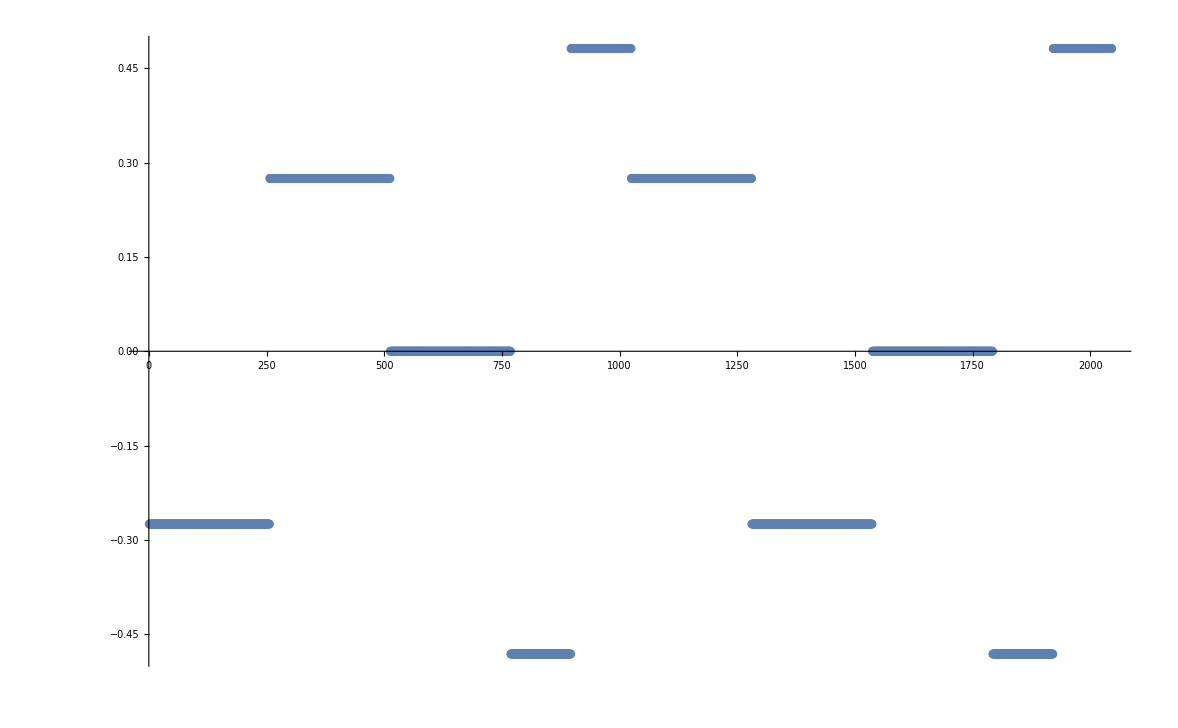

```mathematica
ListPlot[Table[Im[soln[[n,2]][[2]][[1]][[2]][[1]]],{n,1,2045}]]
```

```mathematica
soln[[513,2]][[2]][[1]][[2]][[1]]
```

2.40213

```mathematica
soln[[513]]
```

{t0109→ConditionalExpression[1. (-2.35619+6.28319 C[1]),C[1]∈ℤ],t0110→ConditionalExpression[1. (2.40213+6.28319 C[2]),C[2]∈ℤ],t0111→ConditionalExpression[1. (0.592985+6.28319 C[3]),C[3]∈ℤ],t0203→ConditionalExpression[1. (-2.35619+6.28319 C[4]),C[4]∈ℤ],t0204→ConditionalExpression[1. (2.40213+6.28319 C[5]),C[5]∈ℤ],t0205→ConditionalExpression[1. (0.592985+6.28319 C[6]),C[6]∈ℤ],t0306→ConditionalExpression[1. (-1.26306+6.28319 C[7]),C[7]∈ℤ],t0307→ConditionalExpression[1. (-0.761348+6.28319 C[8]),C[8]∈ℤ],t0308→ConditionalExpression[1. (-0.603914+6.28319 C[9]),C[9]∈ℤ],t0309→ConditionalExpression[1. (-2.96303+6.28319 C[10]),C[10]∈ℤ]}

```mathematica
Table[{soln[[513,n]][[1]],soln[[513,n]][[2]][[1]][[2]][[1]]},{n,1,10}]
```

{{t0109,-2.35619},{t0110,2.40213},{t0111,0.592985},{t0203,-2.35619},{t0204,2.40213},{t0205,0.592985},{t0306,-1.26306},{t0307,-0.761348},{t0308,-0.603914},{t0309,-2.96303}}

```mathematica
Sin[0.5929848849224502`100]
```

0.5588388030762858874050951188173697979477012160786616465812477875331422801243669268666197796678638113

```mathematica
(r1103/.{t0102->Pi/2,t0103->Pi/2,t0104->Pi/2,t0105->Pi/2,t0106->Pi/2,t0107->Pi/2,
t0211->0,t0210->0,t0209->0,t0206->0,t0205->0,t0204->0,
t0311->0,t0310->0,t0309->0,t0308->0,t0307->0

})[[1;;11,1;;3]]//MatrixForm
```

(0 | -Cos[t0203] Cos[t0207] Cos[t0208] | Cos[t0304] Cos[t0305] Cos[t0306] Sin[t0203]
0 | -Cos[t0207] Cos[t0208] Sin[t0203] | -Cos[t0203] Cos[t0304] Cos[t0305] Cos[t0306]
0 | 0 | -Cos[t0305] Cos[t0306] Sin[t0304]
0 | 0 | -Cos[t0306] Sin[t0305]
0 | 0 | -Sin[t0306]
0 | -Cos[t0208] Sin[t0207] | 0
Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0111] | -Sin[t0108] Sin[t0208] | 0
Cos[t0109] Cos[t0110] Cos[t0111] Sin[t0108] | Cos[t0108] Sin[t0208] | 0
Cos[t0110] Cos[t0111] Sin[t0109] | 0 | 0
Cos[t0111] Sin[t0110] | 0 | 0
Sin[t0111] | 0 | 0)

```mathematica
roln=NSolve[{
Sin[t0111]==Cos[t0111] Sin[t0110],
Cos[t0111] Sin[t0110]==Cos[t0110] Cos[t0111] Sin[t0109],
Cos[t0110] Cos[t0111] Sin[t0109]==Cos[t0109] Cos[t0110] Cos[t0111] Sin[t0108]+Cos[t0108] Sin[t0208],
Cos[t0109] Cos[t0110] Cos[t0111] Sin[t0108]+Cos[t0108] Sin[t0208]==Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0111]+Cos[t0108] Sin[t0208],
Cos[t0108] Cos[t0109] Cos[t0110] Cos[t0111]+Cos[t0108] Sin[t0208]==Cos[t0208] Sin[t0207],
Cos[t0208] Sin[t0207]==Sin[t0306],
Sin[t0306]==Cos[t0306] Sin[t0305],
Cos[t0306] Sin[t0305]==Cos[t0305] Cos[t0306] Sin[t0304],
Cos[t0305] Cos[t0306] Sin[t0304]==Cos[t0207] Cos[t0208] Sin[t0203]+Cos[t0203] Cos[t0304] Cos[t0305] Cos[t0306],
Cos[t0207] Cos[t0208] Sin[t0203]+Cos[t0203] Cos[t0304] Cos[t0305] Cos[t0306]==Cos[t0304] Cos[t0305] Cos[t0306] Sin[t0203]+Cos[t0203] Cos[t0207] Cos[t0208]
}]
```

{1}
 |  |  |  |

```mathematica
Length[roln]
```

1024

```mathematica
roln[[1]]
```

{t0108→ConditionalExpression[1. (-2.35619+6.28319 C[1]),C[1]∈ℤ],t0109→ConditionalExpression[1. (-0.339837+6.28319 C[2]),C[2]∈ℤ],t0110→ConditionalExpression[1. (-0.321751+6.28319 C[3]),C[3]∈ℤ],t0111→ConditionalExpression[1. (-0.306277+6.28319 C[4]),C[4]∈ℤ],t0203→ConditionalExpression[1. (-1.03808+6.28319 C[5]),C[5]∈ℤ],t0207→ConditionalExpression[1. (-0.339837+6.28319 C[6]),C[6]∈ℤ],t0208→ConditionalExpression[1. (-0.440511+6.28319 C[7]),C[7]∈ℤ],t0304→ConditionalExpression[1. (-0.339837+6.28319 C[8]),C[8]∈ℤ],t0305→ConditionalExpression[1. (-0.321751+6.28319 C[9]),C[9]∈ℤ],t0306→ConditionalExpression[1. (-0.306277+6.28319 C[10]),C[10]∈ℤ]}

```mathematica
Table[{soln[[513,n]][[1]],soln[[513,n]][[2]][[1]][[2]][[1]]},{n,1,10}]
```

{{t0109,-2.35619},{t0110,2.40213},{t0111,0.592985},{t0203,-2.35619},{t0204,2.40213},{t0205,0.592985},{t0306,-1.26306},{t0307,-0.761348},{t0308,-0.603914},{t0309,-2.96303}}

```mathematica
Table[{roln[[1,n]][[1]],soln[[513,n]][[2]][[1]][[2]][[1]]},{n,1,10}]
```

{{t0108,-2.35619},{t0109,2.40213},{t0110,0.592985},{t0111,-2.35619},{t0203,2.40213},{t0207,0.592985},{t0208,-1.26306},{t0304,-0.761348},{t0305,-0.603914},{t0306,-2.96303}}